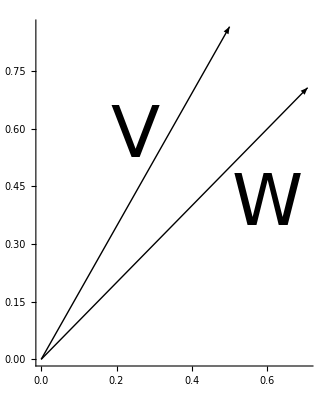

```mathematica
V[ϕ_]:={Sin[ϕ],Cos[ϕ]};
W[θ_]:={Cos[θ],Sin[θ]};
V1 = Graphics[{Arrow[{{0,0},V[Pi/6]}],Text[Style["V",72],{.25,Sqrt[3]/3}]}];
W1=Graphics[{Arrow[{{0,0},W[Pi/4]}],Text[Style["W",72],{.6,.4}]}];
Show[V1,W1,Axes->True]
```

```mathematica
.5+.25*FullSimplify[Tr[Sqrt[ConjugateTranspose[Outer[Times,V[x],V[x]]-Outer[Times,W[y],W[y]]].(Outer[Times,V[x],V[x]]-Outer[Times,W[y],W[y]])]],Assumptions->y∈Reals&&x∈Reals]
```

0.5+0.5 Abs[Cos[x+y]]

```mathematica
A = {{.5,.5},{.5,.5}}
B=.5{{1,0},{0,1}}
Tr[A*MatrixLog2[A]]
```

{{0.5,0.5},{0.5,0.5}}

{{0.5,0.},{0.,0.5}}

1. MatrixLog2[{{0.5,0.5},{0.5,0.5}}]

```mathematica
Tr[B*Log2[B]]
```

-1.